# Z trapping estimation

## Using that the sphere is trapped in a gaussian beam, calculating a back of the hand approximation for how much power is incident on the sphere.

Useful Constants (in

```mathematica
w0 = 12
λ = 1.064
zR = π*w0^2 / λ
w[z_]:=w0 * Sqrt[1+(z/zR)^2]
rsphere = 5
```

12

1.064

425.178

5

Calculate the power felt by the sphere distance z from waist and of radius r (not quite right since not really in paraxial approximation)

```mathematica
P0=1
P[ z_]:= P0*(1-Exp[-2*rsphere^2  / w[z]^2])
```

1

```mathematica
P'[z]
```

-(3.84146×10^-6 ⅇ^(-25/(72 (1+5.5317×10^-6 z^2))) z)/((1+5.5317×10^-6 z^2)^2)

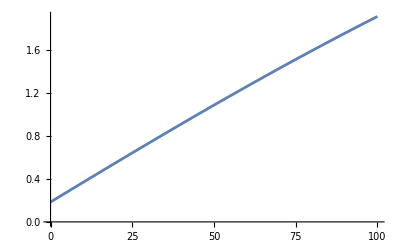

```mathematica
Pdiff[x_,δ_] :=(P[x+δ] - P[x])/P[x]*100
Plot[Abs[Pdiff[x,20]],{x,0,100}]
```

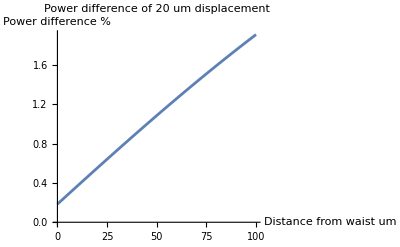

```mathematica
Show[%20,AxesLabel->{HoldForm[Distance from waist um],HoldForm[Power difference %]},PlotLabel->HoldForm[Power difference of 20 um displacement],LabelStyle->{GrayLevel[0]}]
```

The resonant frequency goes as the square root of the effective spring constant .

```mathematica
wi = 30
fp[wf_] := wf^2 - wi^2 
fp[160]
```

30

24700